## Utility functions

```mathematica
(* string substitution *)
Sub[rule_,init_String,l_Integer]:=Nest[StringReplace[#,rule]&,init,l]
```

```mathematica
(* Height (integrated arrow field), can also be seen as the mode k=0 of the Fourier transform of the sequence of arrows *)
Heights[arrows_]:=Table[Total[arrows[[;;N]]],{N,1,Length[arrows]}];
```

```mathematica
(* maximum of the height distribution *)
MaxHeights[heights_]:=Block[{absheights=Abs[heights]},Table[Max[absheights[[;;N]]],{N,1,Length[heights]}]];
```

```mathematica
(* for a string of an even number of A and B, replace every couple by the corresponding arrow *)
ToArrowAlphabet[string_]:=StringReplace[string,{"AB"->"R","BA"->"L","AA"->"Ia","BB"->"Ib"}];
(* return the vector counting the number of arrows *)
ArrowCountVec[string_]:=StringCount[string,#]&/@{"R","L","Ia","Ib"};
```

```mathematica
(* periodic approximant of a sequence seq of two letters, in normal numbering *)
h[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];
(* boundary conditions for the nearest neighbour hoppings *)
PrependTo[tbl,{1,n}->jump[n]];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

For the E=0 level to exist, we need an odd number of letters. But we also need the system to be bipartite for the wavefunction to be nonzero only on one site over two → open boundary conditions.

```mathematica
(* open approximant of a sequence seq of two letters, in normal numbering *)
ho[ρ_,seq_]:=Block[{jump,tbl,ar,n=StringLength[seq]},
jump[j_]:=If[StringTake[seq,{j}]=="B",1.,ρ];

(* nearest neighbour hopppings *)
tbl=Table[{i,i+1}->jump[i],{i,1,n-1}];

(* transform to an array and construct the lower diagonal part *)
ar=SparseArray[tbl,{n,n}];
Normal[ar+ConjugateTranspose[ar]]
]
```

## Fibonacci substitution

```mathematica
(* inflation matrix on the arrows of the Fibonacci chain *)
M={{2,1,2},{1,2,2},{1,1,1}};
```

```mathematica
M//MatrixForm
```

(2 | 1 | 2
1 | 2 | 2
1 | 1 | 1)

```mathematica
Eigensystem[M]
```

{{2+√5,1,2-√5},{{1/2 (1+√5),1/2 (1+√5),1},{-1,1,0},{1/2 (1-√5),1/2 (1-√5),1}}}

```mathematica
(* whithout surprise the largest eigenvalue is τ^3 *)
((1+√5)/2)^3//Expand
```

2+√5

```mathematica
(* Fibonacci substitution *)
FiboSub[l_,C0_String]:=Sub[{"A"->"AB","B"->"A"},C0,l];
(* Fibonacci substitution, composed 3 times *)
FiboSub3[l_,C0_String]:=Sub[{"A"->"ABABA","B"->"ABA"},C0,l];
ArrowSub[l_,C0_String]:=Sub[{"R"->"RILL","L"->"RILR","I"->"RILLR"},C0,l];
FiboArrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"I"->0};
LocalEnvs={"RR","RI","LL","IL","LR"};
HeightCount[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs;
LocalEnvs2={"R","L","I"};
HeightCount2[ArrowString_]:=StringCount[ArrowString,#]&/@LocalEnvs2;
(* the field of arrows *)
FiboArrows[l_]:=StringPartition[FiboSub3[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0};
```

```mathematica
FiboSub[10,"A"]
```

ABAABABAABAABABAABABAABAABABAABAABABAABABAABAABABAABABAABAABABAABAABABAABABAABAABABAABAABABAABABAABAABABAABABAABAABABAABAABABAABABAABAABABAABABA

### Numerical study of the heights

```mathematica
ToArrowAlphabet@FiboSub3[1,#]&/@{"AB","BA","AA","BB"}
```

{RRIaL,RIaLL,RRIaLL,RIaL}

```mathematica
ToArrowAlphabet@FiboSub[3,#]&/@{"AB","BA","AA","BB"}
```

{RIaLL,RIaLR,RIaLLR,RIaL}

```mathematica
(* inflation matrix *)
FiboM=ArrowCountVec@ToArrowAlphabet@FiboSub[3,#]&/@{"AB","BA","AA","BB"};
FiboM=Transpose[FiboM];
FiboM//MatrixForm
(* the "BB"="Ib" sequence is not allowed, so we can drop the last line and columns of the matrix*)
FiboM=FiboM[[;;3,;;3]];
FiboM//MatrixForm
```

(1 | 2 | 2 | 1
2 | 1 | 2 | 1
1 | 1 | 1 | 1
0 | 0 | 0 | 0)

(1 | 2 | 2
2 | 1 | 2
1 | 1 | 1)

```mathematica
{sp,vecs}=Eigensystem[FiboM]
(* change of basis matrix *)
P=Transpose[vecs];
PI=Inverse[P]//Simplify;
```

{{2+√5,-1,2-√5},{{(2 (2+√5))/(3+√5),(2 (2+√5))/(3+√5),1},{-1,1,0},{(2 (-2+√5))/(-3+√5),(2 (-2+√5))/(-3+√5),1}}}

```mathematica
PI//MatrixForm
```

(1/(2 √5) | 1/(2 √5) | 1/10 (5-√5)
-1/2 | 1/2 | 0
-1/(2 √5) | -1/(2 √5) | 1/10 (5+√5))

```mathematica
PI.FiboM.P//Simplify//MatrixForm
```

(2+√5 | 0 | 0
0 | -1 | 0
0 | 0 | 2-√5)

```mathematica
arrows=FiboArrows[7];
FiboHeights=Heights[arrows];
```

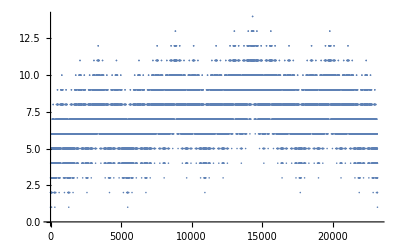

```mathematica
(* the height max grows logarithmically, and the height function goes to 0 arbitrarily far from the origin *)
ListPlot[FiboHeights]
```

```mathematica
FiboMaxs=MaxHeights[FiboHeights];
```

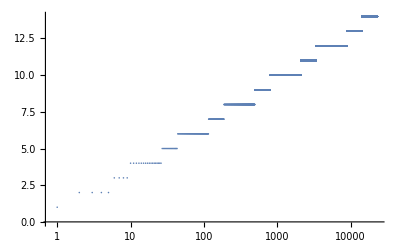

```mathematica
(* the height max grows logarithmically! *)
ListLogLinearPlot[FiboMaxs,PlotRange->All]
```

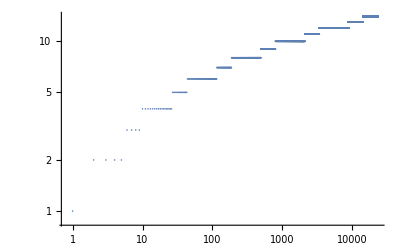

```mathematica
(* the height max doesn't grow like a power-law *)
ListLogLogPlot[FiboMaxs,PlotRange->All]
```

### Generalized inflation matrix

```mathematica
(* First we work with first neighbors local environments *)
LocalEnvs
```

{RR,RI,LL,IL,LR}

```mathematica
{"RL","LI","IR","II"}
```

{RL,LI,IR,II}

```mathematica
(* we obtain the inflation matrix for these environments straightforwardly by counting them *)
A=HeightCount/@(ArrowSub[1,#]&/@LocalEnvs);
Transpose[A]//MatrixForm
```

(0 | 0 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2
2 | 2 | 0 | 1 | 1
2 | 2 | 2 | 2 | 2
1 | 2 | 2 | 2 | 1)

```mathematica
(* but weirdly, the matrix has eigenvalues in a different algebraic field *)
Eigensystem[Transpose[A]]
```

{{1/2 (7+√65),-1,-1,1/2 (7-√65),0},{{(4 (89+11 √65))/(5 (185+23 √65)),(8 (137+17 √65))/(5 (185+23 √65)),-(-655-81 √65)/(5 (185+23 √65)),(8 (137+17 √65))/(5 (185+23 √65)),1},{0,0,-1,0,1},{0,0,0,0,0},{(4 (-89+11 √65))/(5 (-185+23 √65)),(8 (-137+17 √65))/(5 (-185+23 √65)),-(655-81 √65)/(5 (-185+23 √65)),(8 (-137+17 √65))/(5 (-185+23 √65)),1},{-1,1,0,-1,1}}}

```mathematica
(* secondly, we look at local environments defined by "the letter at the right of the current site" *)
LocalEnvs2
```

{R,L,I}

```mathematica
(* the inflation matrix this time has eigenvalues in the expected field *)
A=HeightCount2/@(ArrowSub[1,#]&/@LocalEnvs2);
Transpose[A]//MatrixForm
Eigensystem[Transpose[A]]
```

(1 | 2 | 2
2 | 1 | 2
1 | 1 | 1)

{{2+√5,-1,2-√5},{{(2 (2+√5))/(3+√5),(2 (2+√5))/(3+√5),1},{-1,1,0},{(2 (-2+√5))/(-3+√5),(2 (-2+√5))/(-3+√5),1}}}

```mathematica
(* a dictionary from envs to indices *)
envs={"R","L","I"};
Idx=<|"R"->1,"L"->2,"I"->3|>;
inflatedEnvs=ArrowSub[1,#]&/@envs;
inflatedArrows=({0}~Join~FiboArrows2[#][[;;-2]])&/@inflatedEnvs;
inflatedHeights=Table[Total[#[[;;L]]],{L,1,Length[#]}]&/@inflatedArrows;
RowsHeights=MapThread[{#1,#2}&,{inflatedEnvs,inflatedHeights}];
(* construct the matrices *)
table0=Table[0,{i,1,3},{j,1,3}];
T2left=table0;
T20=table0;
T2right=table0;
(* a way of constructing the generalized matrices automatically *)
For[col=1,col≤3,col++,
{rows,heights}=RowsHeights[[col]];
rows=StringPartition[rows,1];
For[i=1,i≤Length[rows],i++,
h=heights[[i]];
row=Idx[rows[[i]]];
If[h==-1,
T2left[[row,col]]+=1,
If[h==0,
T20[[row,col]]+=1,
If[h==1,
T2right[[row,col]]+=1]]]
]
]
```

```mathematica
T2right//MatrixForm
```

(0 | 0 | 0
1 | 1 | 1
1 | 1 | 1)

```mathematica
T2left==Tleft
T2right==Tright
T20==T0
```

{{0,0,1},{0,0,0},{0,0,0}}==Tleft

{{0,0,0},{1,1,1},{1,1,1}}==Tright

{{1,2,1},{1,0,1},{0,0,0}}==T0

```mathematica
(* generalized inflation matrices for height dependent environments *)
T0={{1,2,1},{1,0,1},{0,0,0}};
Tright={{0,0,0},{1,1,1},{1,1,1}};
Tleft={{0,0,1},{0,0,0},{0,0,0}};
(* Legendre transform of the inflation matrix *)
T[z_]:=z T2left+T20+z^-1 T2right
(* Generating matrix of the height distribution *)
TT[z_]:=T[1/z].T[z]
```

```mathematica
(* Perron-Frobenius eigenvalue of TT is a perfect square: see height_distro_fibonacci.nb for more details *)
Simplify[(((1+z)^2+√((1+z)^4+4 z^2))/(2z))^2==(1+4 z+8 z^2+4 z^3+z^4+(1+z)^2 √(1+4 z+10 z^2+4 z^3+z^4))/(2 z^2),{z>0}]
```

True

```mathematica
FullSimplify[√((1+4 z+8 z^2+4 z^3+z^4+(1+z)^2 √(1+4 z+10 z^2+4 z^3+z^4))/(2 z^2)),{z>0}]
```

(√(1+4 z+8 z^2+4 z^3+z^4+(1+z)^2 √(1+z (4+z (10+z (4+z))))))/(√2 z)

## Ag substitution

```mathematica
AgSub[l_,C0_String]:=Sub[{"A"->"AAB","B"->"A"},C0,l];
(* the field of arrows *)
AgArrows[l_]:=StringPartition[AgSub[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
```

```mathematica
AgSub[5,"B"]
```

AABAABAAABAABAAABAABAABAAABAABAAABAABAABA

```mathematica
(* we have to iterate only 1 time to obtain an effective substitution acting on the arrows *)
n=1;
AgSub[n,"B"]
StringLength[%]
AgSub[n,"A"]
StringLength[%]
```

A

1

AAB

3

```mathematica
(* inflation matrix *)
AgM=ArrowCountVec@ToArrowAlphabet@AgSub[1,#]&/@{"AB","BA","AA","BB"};
AgM=Transpose[AgM];
AgM//MatrixForm
(* the "BB" environment is forbidden, so we can drop it *)
AgM=AgM[[;;3,;;3]];
AgM//MatrixForm
```

(0 | 1 | 1 | 0
1 | 0 | 1 | 0
1 | 1 | 1 | 1
0 | 0 | 0 | 0)

(0 | 1 | 1
1 | 0 | 1
1 | 1 | 1)

```mathematica
(* the spectrum is like the Fibo one: the 2 algebraically conjugate numbers and -1 *)
Eigensystem[AgM]
```

{{1+√2,-1,1-√2},{{-(-1-√2)/(2+√2),-(-1-√2)/(2+√2),1},{-1,1,0},{-(1-√2)/(-2+√2),-(1-√2)/(-2+√2),1}}}

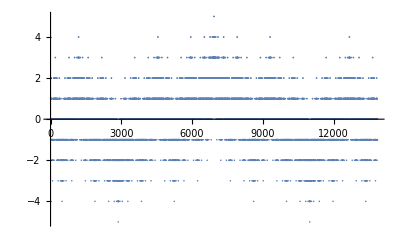

```mathematica
arrows=AgArrows[11];
AgHeights=Heights[arrows];
(* the height function goes to 0 arbitrarily far from the origin *)
ListPlot[AgHeights,PlotRange->All]
```

```mathematica
AgMaxs=MaxHeights[AgHeights];
```

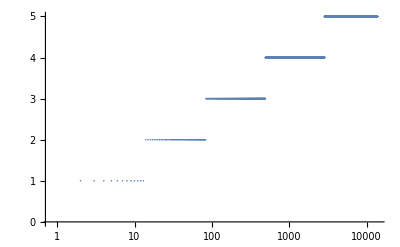

```mathematica
(* the height max grows logarithmically! *)
ListLogLinearPlot[AgMaxs,PlotRange->All]
```

```mathematica
mat=ho[ρ,AgSub[9,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

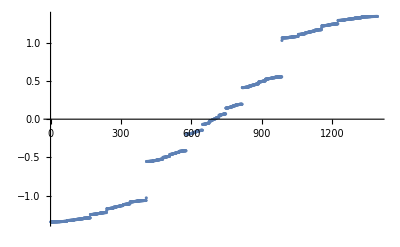

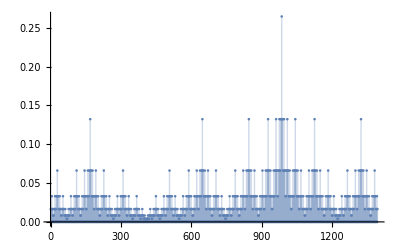

```mathematica
ListPlot[vals]
idxCenter=(Length[vals]+1)/2;
ListPlot[Abs@vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

## B2 substitution (periodic?)

```mathematica
B2Sub[l_,C0_String]:=Sub[{"A"->"ABB","B"->"A"},C0,l];
(* the field of arrows *)
B2Arrows[l_,C0_String]:=StringPartition[B2Sub[l,C0],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
B2Arrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"a"->0,"b"->0};
```

```mathematica
(* effective susbstitution for the arrows *)
B2ArrowSub[l_,C0_String]:=Sub[{"R"->"RL","L"->"ab","a"->"RLb","b"->"a"},C0,l];
```

```mathematica
(* check that is effective substitution works *)
l=5;
StringPartition[B2ArrowSub[l,"R"],1]
StringPartition[B2Sub[l,"AB"],2]/.{"AB"->"R","BA"->"L","AA"->"a","BB"->"b"}
```

{R,L,a,b,R,L,b,a,R,L,a,b,a,R,L,b,R,L,a,b,R,L,b,a,R,L,b,R,L,a,b,a}

{R,L,a,b,R,L,b,a,R,L,a,b,a,R,L,b,R,L,a,b,R,L,b,a,R,L,b,R,L,a,b,a}

```mathematica
M={{1,1},{2,0}};
```

```mathematica
Eigensystem[M]
```

{{2,-1},{{1,1},{-1,2}}}

```mathematica
(* we have to iterate at just 1 time to obtain an effective substitution acting on the arrows! *)
n=1;
B2Sub[n,"B"]
StringLength[%]
B2Sub[n,"A"]
StringLength[%]
```

A

1

ABB

3

```mathematica
(* inflation matrix *)
B2M=ArrowCountVec@ToArrowAlphabet@B2Sub[1,#]&/@{"AB","BA","AA","BB"};
B2M=Transpose[B2M];
B2M//MatrixForm
```

(1 | 0 | 1 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 1 | 1 | 0)

```mathematica
M={{1,1,1},{1,0,1},{0,1,0}};
Eigensystem[M]
```

{{2,-1,0},{{3,2,1},{0,-1,1},{-1,0,1}}}

### Numerical study of the arrow field

```mathematica
arrows=B2Arrows[6,"AB"];
B2Heights=Heights[arrows];
```

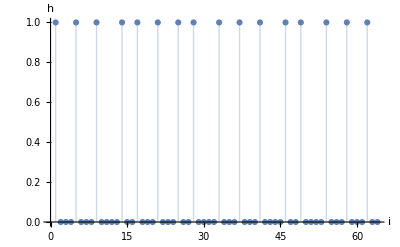

/home/nicolas/git/articles/electronic_wavefunctions/notes/height_b2.pdf

```mathematica
(* the height function goes to 0 arbitrarily far from the origin *)
ListPlot[B2Heights,PlotRange->All,Filling->Axis,AxesLabel->{"i","h"}]
Export[NotebookDirectory[]<>"notes/height_b2.pdf",%]
```

```mathematica
mat=ho[0.5,B2Sub[10,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

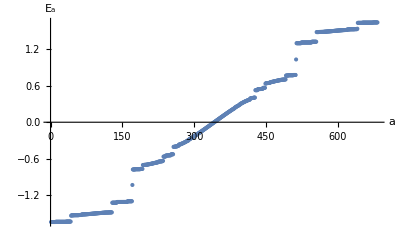

/home/nicolas/git/articles/electronic_wavefunctions/notes/spec_b2.pdf

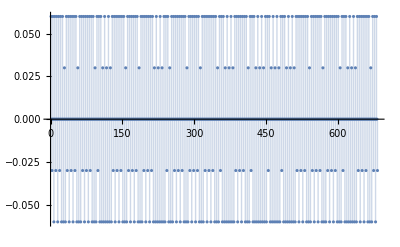

```mathematica
ListPlot[vals,AxesLabel->{"a","E_a"}]
Export[NotebookDirectory[]<>"notes/spec_b2.pdf",%]
idxCenter=(Length[vals]+1)/2;
ListPlot[vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

## B3 substitution (simplest example of non-Pisot)

```mathematica
Mnp={{1,1},{3,0}};
```

```mathematica
Eigenvalues[Mnp]
%//N
```

{1/2 (1+√13),1/2 (1-√13)}

{2.30278,-1.30278}

```mathematica
(* B3 substitution *)
B3Sub[l_,C0_String]:=Sub[{"A"->"ABBB","B"->"A"},C0,l];
(* B3 substitution, composed 3 times *)
B3Sub3[l_,C0_String]:=Sub[{"A"->"ABBBAAAABBBABBBABBB","B"->"ABBBAAA"},C0,l];
(* the field of arrows *)
B3Arrows[l_]:=StringPartition[B3Sub3[l,"AB"],2]/.{"AB"->1,"BA"->-1,"AA"->0,"BB"->0};
B3ArrowSub[l_,C0_String]:=Sub[{"R"->"RbaabLbLbLbLa","L"->"RbaabLaRbRbRb","a"->"RbaabLbLbLbLaRbRbRb","b"->"RbaabLa"},C0,l];
B3Arrows2[string_]:=StringPartition[string,1]/.{"R"->1,"L"->-1,"a"->0,"b"->0};
```

### Behavior of the heights

```mathematica
(* we have to iterate at least 3 times to obtain an effective substitution acting on the arrows *)
n=3;
B3Sub[n,"B"]
StringLength[%]
B3Sub[n,"A"]
StringLength[%]
```

ABBBAAA

7

ABBBAAAABBBABBBABBB

19

```mathematica
(* inflation matrix for the arrows *)
ToArrowAlphabet@B3Sub3[1,"AB"]
ToArrowAlphabet@B3Sub3[1,"BA"]
ToArrowAlphabet@B3Sub3[1,"AA"]
ToArrowAlphabet@B3Sub3[1,"BB"]
```

RIbIaIaIbLIbLIbLIbLIa

RIbIaIaIbLIaRIbRIbRIb

RIbIaIaIbLIbLIbLIbLIaRIbRIbRIb

RIbIaIaIbLIa

```mathematica
(* inflation matrix *)
B3M=ArrowCountVec@ToArrowAlphabet@B3Sub3[1,#]&/@{"AB","BA","AA","BB"};
B3M=Transpose[B3M];
B3M//MatrixForm
```

(1 | 4 | 4 | 1
4 | 1 | 4 | 1
3 | 3 | 3 | 3
5 | 5 | 8 | 2)

```mathematica
((1-√13)/2)^3//Expand//FullSimplify
```

5-2 √13

```mathematica
B3subM={{1,1},{3,0}};
MatrixPower[B3subM,3]
```

{{7,4},{12,3}}

```mathematica
Log[(1+√13)/3]//N
```

0.42865

```mathematica
Eigensystem[B3M]
```

{{5+2 √13,-3,5-2 √13,0},{{-(-133-37 √13)/(2 (4+√13) (17+5 √13)),-(-133-37 √13)/(2 (4+√13) (17+5 √13)),(3 (4+√13))/(17+5 √13),1},{-1,1,0,0},{-(-133+37 √13)/(2 (-4+√13) (-17+5 √13)),-(-133+37 √13)/(2 (-4+√13) (-17+5 √13)),(3 (-4+√13))/(-17+5 √13),1},{-1,-1,1,1}}}

```mathematica
freqs={-(-133-37 √13)/(2 (4+√13) (17+5 √13)),-(-133-37 √13)/(2 (4+√13) (17+5 √13)),(3 (4+√13))/(17+5 √13),1};
freqs=freqs/Norm[freqs,1]//Expand//FullSimplify
```

{1/18 (7-√13),1/18 (7-√13),1/9 (-5+2 √13),1/9 (7-√13)}

```mathematica
arrows=B3Arrows[4];
B3Heights=Heights[arrows];
```

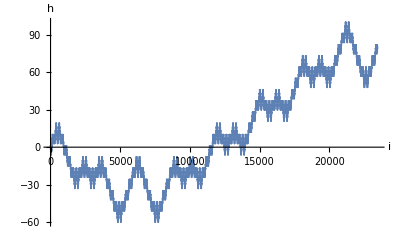

/home/nicolas/git/articles/electronic_wavefunctions/notes/height_b3.pdf

```mathematica
(* the height function *)
ListPlot[B3Heights,AxesLabel->{"i","h"}]
Export[NotebookDirectory[]<>"notes/height_b3.pdf",%]
```

```mathematica
mat=ho[0.5,B3Sub[10,"B"]];
{vals,vecs}=Eigensystem[mat];
o=Ordering[vals];
vals=vals[[o]];
vecs=vecs[[o]];
```

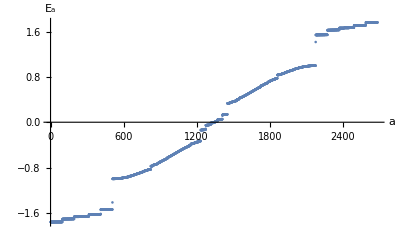

/home/nicolas/git/articles/electronic_wavefunctions/notes/spec_b3.pdf

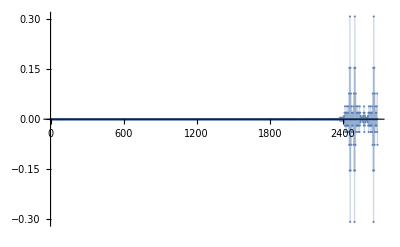

```mathematica
ListPlot[vals,AxesLabel->{"a","E_a"}]
Export[NotebookDirectory[]<>"notes/spec_b3.pdf",%]
idxCenter=(Length[vals]+1)/2;
ListPlot[vecs[[idxCenter]],Filling->Axis,PlotRange->All]
```

```mathematica
(* the height function goes to 0 arbitrarily far from the origin *)
ρ=0.5;
ListPlot[ρ^B3Heights,Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
B3Maxs=MaxHeights[B3Heights];
```

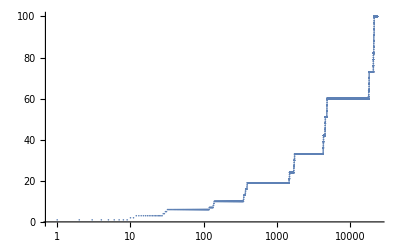

```mathematica
(* the height max doesn't grow logarithmically *)
ListLogLinearPlot[B3Maxs,PlotRange->All]
```

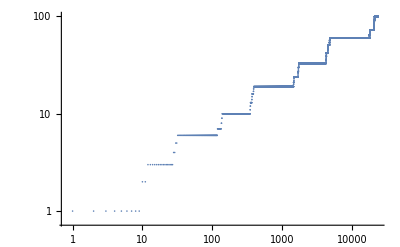

```mathematica
(* the height max grows like a power-law! *)
ListLogLogPlot[B3Maxs,PlotRange->All]
```

```mathematica
data=MapThread[{Log[#1],Log[#2]}&,{Range[Length[B3Maxs]],B3Maxs}];
```

0.113886+0.429665 x

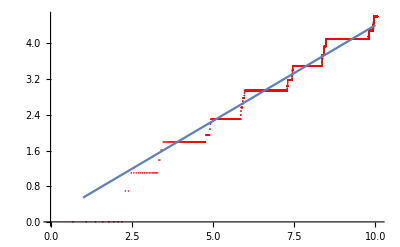

```mathematica
line=Fit [data,{1,x},x]
Show[ListPlot[data, PlotStyle->Red], Plot[line, {x, 1, 10}]]
```

```mathematica
(* theoretical prediction for the slope (see the notes for the details) *)
Log[3]/Log[(1/2 (1+√13))^3]//N
```

0.439033

```mathematica
(* chain substitution matrix *)
B3subM={{1,1},{3,0}};
Eigensystem[B3subM]
```

{{1/2 (1+√13),1/2 (1-√13)},{{1/6 (1+√13),1},{1/6 (1-√13),1}}}

```mathematica
(1/6 (1+√13))^-1//FullSimplify
%//N
```

1/2 (-1+√13)

1.30278

### Generalized inflation matrix

```mathematica
(* a dictionary from envs to indices *)
envs={"R","L","a","b"};
Idx=<|"R"->1,"L"->2,"a"->3,"b"->4|>;
inflatedEnvs=B3ArrowSub[1,#]&/@envs;
inflatedArrows=({0}~Join~B3Arrows2[#][[;;-2]])&/@inflatedEnvs;
inflatedHeights=Table[Total[#[[;;L]]],{L,1,Length[#]}]&/@inflatedArrows;
RowsHeights=MapThread[{#1,#2}&,{inflatedEnvs,inflatedHeights}];
(* construct the matrices *)
table0=Table[0,{i,1,4},{j,1,4}];
Clear[T];
(* number of relative height variations we consider *)
Htot=10;
T=Table[table0,{h,-Htot,Htot}];
(* a way of constructing the generalized matrices automatically *)
For[col=1,col≤4,col++,
{rows,heights}=RowsHeights[[col]];
rows=StringPartition[rows,1];
For[i=1,i≤Length[heights],i++,
h=heights[[i]];
row=Idx[rows[[i]]];
T[[Htot+1+h,col,row]]+=1;
]
]
```

```mathematica
Clear[Infl];
Infl[β_]:=β^-3 T[[Htot+1-3]]+β^-2 T[[Htot+1-2]]+β^-1 T[[Htot+1-1]]+T[[Htot+1]]+β^1 T[[Htot+1+1]]+β^2 T[[Htot+1+2]]+β^3 T[[Htot+1+3]]
```

```mathematica
Infl[β_]:=Total@Table[β^(idxH-Htot-1)T[[idxH]],{idxH,1,2Htot+1}]
```

```mathematica
sps=Table[Sort[Eigenvalues[Infl[β]]],{β,0.1,1.,0.01}];
```

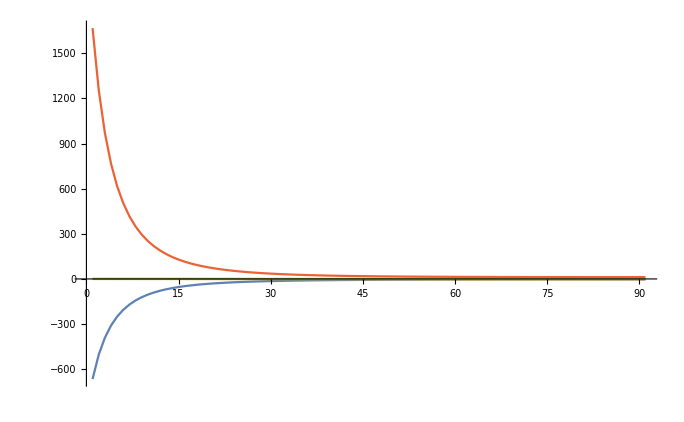

```mathematica
ListPlot[Transpose@sps,Joined->True,PlotRange->All]
```

```mathematica
Transpose[B3M]==Infl[1]
```

True

```mathematica
Infl[β]//MatrixForm
```

(1 | 1+1/β^2+1/β+β | 1/β^3+2 β | 1+1/β^2+1/β+2 β
2+β+β^2 | β | 1+2 β | 3 β+β^2+β^3
1+1/β^3+1/β^2+1/β | 1+1/β^2+1/β+β | 1/β^3+2 β | 2+2/β^2+2/β+2 β
1 | β | 1+2 β | 2 β)

```mathematica
Eigensystem[Infl[β]];
%/.β->1//N
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

{{0.,-3.,-2.2111,12.2111},{{-1.,-1.,0.,1.},{ComplexInfinity,Indeterminate,-2.,1.},{-0.151388,-0.151388,-1.30278,1.},{1.65139,1.65139,2.30278,1.}}}

```mathematica
vec[β_]:=Eigensystem[Infl[β]][[2]][[-4]]
```

```mathematica
val[β_]:=Eigensystem[Infl[β]][[1]][[-4]]
```

```mathematica
val[i_,β_]:=Eigensystem[Infl[x]][[1]][[i]]/.x->β
```

```mathematica
Plot[val[2,β],{β,0,10}]
```

$Aborted

```mathematica
val[x]
```

0

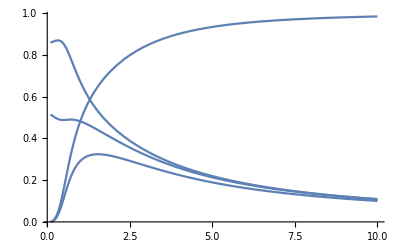

```mathematica
Plot[Abs@vec[β],{β,0.1,10},PlotRange->All,Filling->None]
```

```mathematica
12.21110255092798
```

```mathematica
Eigensystem[B3M]//N
```

{{12.2111,-3.,-2.2111,0.},{{0.5,0.5,0.651388,1.},{-1.,1.,0.,0.},{0.5,0.5,-1.15139,1.},{-1.,-1.,1.,1.}}}

## NPG substitution (non-Pisot golden ratio substitution)

## Thue-Morse

## nth metallic mean, n even (n = 2k)

```mathematica
K0={{0,1,0},{1,0,1},{k,k,k}};
Km1={{0,0,1},{0,0,0},{0,0,k-1}};
```

```mathematica
ClearAll[T];
T[z_]:=z*Km1+K0;
```

```mathematica
Eigensystem[T[1/z].T[z]]
```

{{1,(k^2+2 z+2 k^2 z+k^2 z^2-k √(k^2+4 z+2 k^2 z+k^2 z^2)-k z √(k^2+4 z+2 k^2 z+k^2 z^2))/(2 z),(k^2+2 z+2 k^2 z+k^2 z^2+k √(k^2+4 z+2 k^2 z+k^2 z^2)+k z √(k^2+4 z+2 k^2 z+k^2 z^2))/(2 z)},{{-1,1,0},{(-k-2 z-k z+√(k^2+4 z+2 k^2 z+k^2 z^2))/((-1+k+z+k z) (-k-k z+√(k^2+4 z+2 k^2 z+k^2 z^2))),-(k z+2 z^2+k z^2-z √(k^2+4 z+2 k^2 z+k^2 z^2))/((-1+k+z+k z) (-k-k z+√(k^2+4 z+2 k^2 z+k^2 z^2))),1},{-(-k-2 z-k z-√(k^2+4 z+2 k^2 z+k^2 z^2))/((-1+k+z+k z) (k+k z+√(k^2+4 z+2 k^2 z+k^2 z^2))),-(-k z-2 z^2-k z^2-z √(k^2+4 z+2 k^2 z+k^2 z^2))/((-1+k+z+k z) (k+k z+√(k^2+4 z+2 k^2 z+k^2 z^2))),1}}}

```mathematica
Simplify[(k^2+2 z+2 k^2 z+k^2 z^2+k √(k^2+4 z+2 k^2 z+k^2 z^2)+k z √(k^2+4 z+2 k^2 z+k^2 z^2))/(2 z),{k>0,z>0}]
```

(2 z+k^2 (1+z)^2+k (1+z) √(4 z+k^2 (1+z)^2))/(2 z)

```mathematica
ω[z_]:=(2 z+k^2 (1+z)^2+k (1+z) √(4 z+k^2 (1+z)^2))/(2 z)
```

```mathematica
Simplify[ω[z]/ω[1/z],{z>0,k>0}]
```

1

```mathematica
Simplify[D[Log[ω[E^β]],{β,2}]/.β->0,{z>0,k>0}]
```

k/(2 √(1+k^2))

## nth metallic mean, n odd (n = 2k+1)

```mathematica
(* k=0 substitution *)
Ak0Sub[l_,C0_String]:=Sub[{"A"->"AB","B"->"A"},C0,l];
(* k=1 substitution *)
Ak1Sub[l_,C0_String]:=Sub[{"A"->"AAAB","B"->"A"},C0,l];
Ak1Arrows[l_,C0_]:=StringPartition[Ak1Sub[l,C0],2]/.{"AB"->1,"BA"->-1,"AA"->0};
```

```mathematica
Ak0Sub[3,"AA"];
StringReplace[%,{"AA"->"u","AB"->"r","BA"->"l"}]
```

rullr

```mathematica
Ak1Sub[3,"AB"];
StringReplace[%,{"AA"->"u","AB"->"r","BA"->"l"}]
```

urururuulululurururuulululul

```mathematica
Ak1Sub[3,"BA"];
StringReplace[%,{"AA"->"u","AB"->"r","BA"->"l"}]
```

urururuulululurururuulululur

```mathematica
Ak1Sub[3,"AA"];
StringReplace[%,{"AA"->"u","AB"->"r","BA"->"l"}]
```

urururuulululurururuululululurururuulululur

### Numerical study of the heights

```mathematica
arrows=Ak1Arrows[9,"AB"];
heights=Heights[arrows];
```

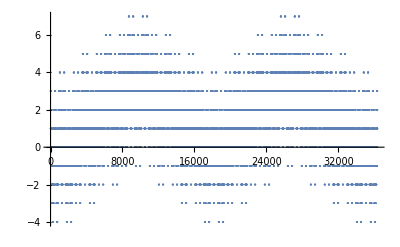

```mathematica
(* the height max grows logarithmically, and the height function goes to 0 arbitrarily far from the origin *)
ListPlot[heights]
```

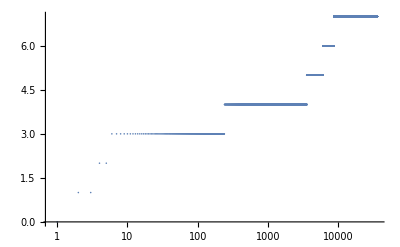

```mathematica
maxheights=MaxHeights[heights];
ListLogLinearPlot[maxheights]
```